```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

### import data

```mathematica
e2List={0,1.1,3};
```

```mathematica
rCoords=Table[Import["inteferencePoints_e2_"<>ToString[e2List[[i]]]<>"_rta.mx"][[1]],{i,Length[e2List]}];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

### plot

```mathematica
colors=ColorData[97,"ColorList"][[7;;]]
```

{RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
colors={RGBColor["#70AD47"],Darker[RGBColor["#70AD47"]],Darker[Darker[RGBColor["#70AD47"]]]};
```

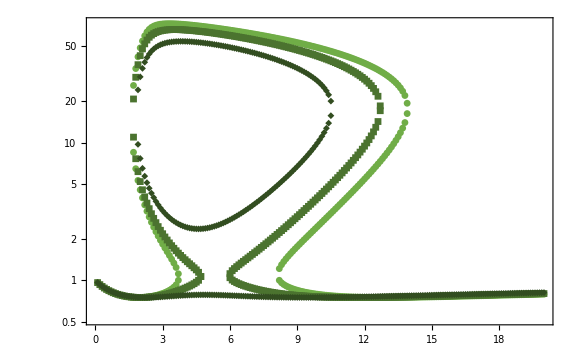

```mathematica
ListLogPlot[rCoords,PlotRange->{Automatic,Automatic},LabelStyle->Directive[Black, 20],Frame->{True,True,False,False},ImageSize->Large,PlotStyle->colors,PlotMarkers->{Automatic,Small}]
```

```mathematica
Export["interferencePlot_mech1.png",%,ImageResolution->200];
```

```mathematica
(*legend plot*)
```

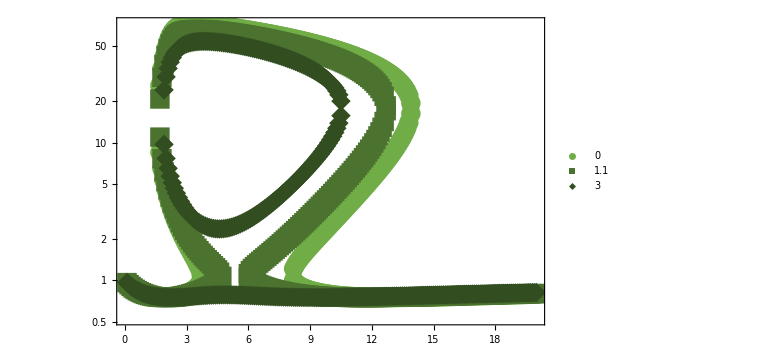

```mathematica
ListLogPlot[rCoords,PlotRange->{Automatic,Automatic},LabelStyle->Directive[Black, 20],PlotLegends->Table[ToString[e2List[[i]]],{i,Length[e2List]}],Frame->{True,True,False,False},ImageSize->Large,PlotStyle->colors,PlotMarkers->{Automatic,Large}]
```

```mathematica
Export["interferencePlot_mech1_legend.png",%,ImageResolution->200];
```